```mathematica
Svodjenje krive drugog reda na kanonski oblik
```

```mathematica
Marija Kostic 286/14
```

```mathematica
Kriva=5-26*a+5*a^2-4*x-4*a*x+8*x^2-26*y+10*a*y-4*x*y+5*y^2;
```

```mathematica
Za parametar a  uzimamo da je a=(broj indeksa) mod 5.
```

```mathematica
a=Mod[286,5]
```

1

```mathematica
Crtamo krivu.
```

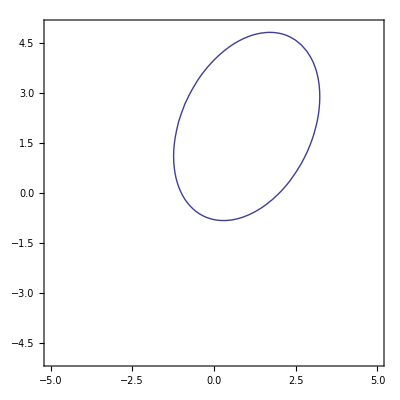

```mathematica
KrivaCrtez=ContourPlot[Kriva==0,{x,-5,5},{y,-5,5},Axes->True]
```

```mathematica
Vektori e1 i e2 su vektori repera u kom kriva ima dati oblik.
```

```mathematica
e1={Red,Arrow[{{0,0},{2,0}}]};
```

```mathematica
e2={Blue,Arrow[{{0,0},{0,2}}]};
```

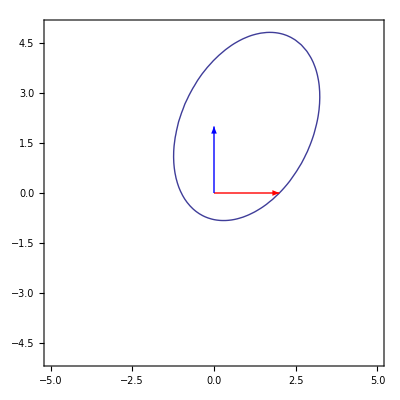

```mathematica
Show[KrivaCrtez,Graphics[{e1,e2}]]
```

```mathematica
Matrica krive:
```

```mathematica
AA={{8,-2},{-2,5}};
```

```mathematica
MatrixForm[AA]
```

(8 | -2
-2 | 5)

```mathematica
Vektor sopstvenih vrednosti i matrica cije su vrste sopstveni vektori koji odgovaraju tim sopstvenim vrednostima:
```

```mathematica
eiSistem=Eigensystem[AA]
```

{{9,4},{{-2,1},{1,2}}}

```mathematica
MatrixForm/@eiSistem
```

{(9
4),(-2 | 1
1 | 2)}

```mathematica
CC=eiSistem[[2]]
```

{{-2,1},{1,2}}

```mathematica
MatrixForm[CC]
```

(-2 | 1
1 | 2)

```mathematica
Kako su sopstveni vektori ortogonalni, treba da ih normiramo. Pravimo funkciju za normiranje na vrste matrice CC.
```

```mathematica
CC=(#/Norm[#])&/@CC
```

{{-2/(√5),1/(√5)},{1/(√5),2/(√5)}}

```mathematica
Matrica prelaska na novu bazu treba da ima sopstvene vektore kao kolone, pa transponujemo matricu.Dobijamo ortogonalnu matricu.
```

```mathematica
CC=Transpose[CC]
```

{{-2/(√5),1/(√5)},{1/(√5),2/(√5)}}

```mathematica
MatrixForm[CC]
```

(-2/(√5) | 1/(√5)
1/(√5) | 2/(√5))

```mathematica
Matrica CC dijagonalizuje matricu AA.
```

```mathematica
Inverse[CC].AA.CC//Simplify//MatrixForm
```

(9 | 0
0 | 4)

```mathematica
Proveravamo da li ova matrica cuva orijentaciju.
```

```mathematica
Det[CC]
```

-1

```mathematica
Dobijamo da je menja.
```

```mathematica
Crtamo nove bazne vektore. Oni su sada kolone matrice CC.ali nam je lakse da uzmemo vrste od transponovane CC.
```

```mathematica
f1v = Transpose[CC][[1]];
f2v = Transpose[CC][[2]];
```

```mathematica
Pravimo odgovarajuce strelice.
```

```mathematica
f1 = {Red, Arrow[{{0,0}, 2f1v}]};
f2 = {Blue, Arrow[{{0,0}, 2f2v}]};
```

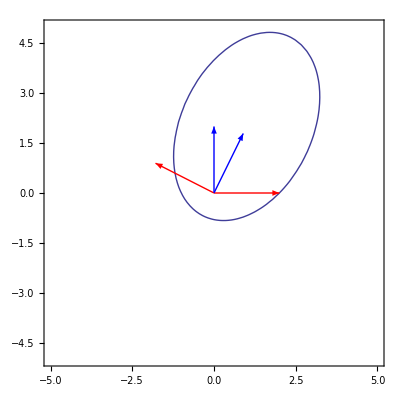

```mathematica
Show[KrivaCrtez, Graphics[{e1,e2}], Graphics[{f1,f2}]]
```

```mathematica
Vidimo da su stara i nova baza raznih orijentacija.Zamenicemo kolone.
```

```mathematica
CC=CC.({{0, 1}, {1, 0}})
```

{{1/(√5),-2/(√5)},{2/(√5),1/(√5)}}

```mathematica
MatrixForm[CC]
```

(1/(√5) | -2/(√5)
2/(√5) | 1/(√5))

```mathematica
Matrica sada ima determinantu 1.
```

```mathematica
Det[CC]
```

1

```mathematica
Promenicemo i vektore koje cemo da crtamo.
```

```mathematica
f1v = Transpose[CC][[1]];
f2v = Transpose[CC][[2]];
f1 = {Red, Arrow[{{0,0}, 2f1v}]};
f2 = {Blue, Arrow[{{0,0}, 2f2v}]};
```

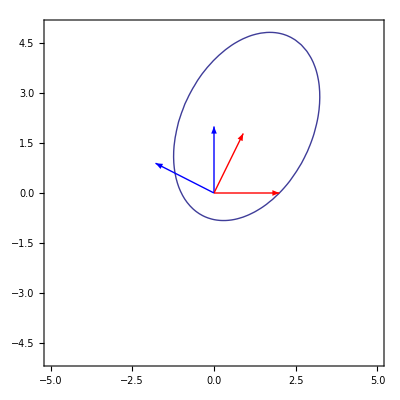

```mathematica
Show[KrivaCrtez, Graphics[{e1,e2}], Graphics[{f1,f2}]]
```

```mathematica
Trazimo transformaciju koordinata koja je odredjena matricom CC.Stare koordinate (x,y) dobijamo mnozenje novih koordinata (xp,yp) matricom CC.
```

```mathematica
CC.{xp,yp}
```

{xp/(√5)-(2 yp)/(√5),(2 xp)/(√5)+yp/(√5)}

```mathematica
U novim, zarotiranim koordinatama, nema clana xp ,yp.
```

```mathematica
Kriva/.{x->xp/(√5)-(2 yp)/(√5),y->(2 xp)/(√5)+yp/(√5)}//Simplify
```

-16-8 √5 xp+4 xp^2+9 yp^2

```mathematica
Kriva1=2Kriva/.{x->xp/(√5)-(2 yp)/(√5),y->(2 xp)/(√5)+yp/(√5)}//Simplify
```

-32-16 √5 xp+8 xp^2+18 yp^2

```mathematica
Sada je potrebno da uradimo translaciju, xs=xp-√5,ys=((3 yp)/2).
```

```mathematica
Kriva1/.{xp->xs+√5,yp->(2 ys)/3}//Simplify
```

8 (-9+xs^2+ys^2)

```mathematica
Vidimo da je kriva xs^2/9+ys^2/9=1, elipsa.
```

```mathematica
Odredjujemo centar krive, iz translacije stavljajuci da je xs=ys=0.
```

```mathematica
CentarKrive=CC.{√5,0}
```

{1,2}

```mathematica
Crtamo reper (xs,ys) u kom kriva ima kanonski oblik.Potrebno je uraditi translaciju do centra. Transliramo pocetnu i krajnju tacku vektora.
```

```mathematica
g1={Red,Arrow[(#+CentarKrive)&/@{{0,0},2f1v}]};
```

```mathematica
g2={Blue,Arrow[(#+CentarKrive)&/@{{0,0},2f2v}]};
```

```mathematica
Crtamo kako izgleda konacni koordinatni sistem gde je crvena osa nova xs osa, a plava nova ys osa.
```

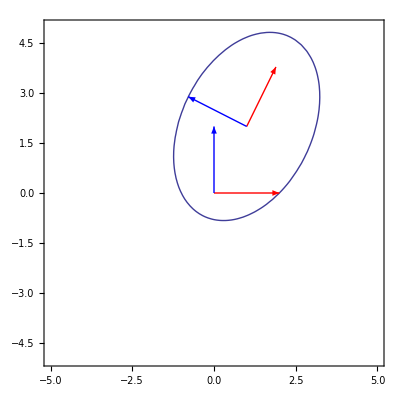

```mathematica
Show[KrivaCrtez,Graphics[{e1,e2}],Graphics[{g1,g2}]]
```